# TextGrid

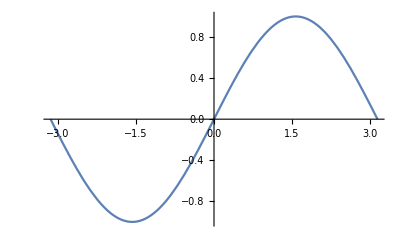
123 | Sin[x] | foobar baz
xyz 123
foo | -Graphics- | 
XXX | 2 x+x^2 |

```mathematica
g=TextGrid[{{123,Sin[x],"foobar baz
xyz 123"},{"foo",Plot[Sin[x],{x,-Pi,Pi}],SpanFromLeft},{"XXX",x^2+2x}},Frame-> All]
```

#### Compare to Grid

```mathematica
Grid[{{123,Sin[x],"foobar baz
xyz 123"},{"foo",Plot[Sin[x],{x,-Pi,Pi}],SpanFromLeft},{"XXX",x^2+2x}},Frame-> All]
```

123 | Sin[x] | foobar baz
xyz 123
foo | -Graphics- | 
XXX | 2 x+x^2 |

### Ctrl+, to add a column; Ctrl+Enter to add a row; Tab to move cursor to next cell; Ctrl+Space to move out of grid

```mathematica
{{□, □, □, □, □}, {123, □, Sin[x], foobar baz
xyz 123, □}, {□, □, □, □, □}, {foo, □, -Graphics-, , □}, {XXX, □, 2 x+x^2, , □}}
```

### Normal

```mathematica
Normal[g]
```

{{123,Sin[x],foobar baz
xyz 123},{foo,-Graphics-},{XXX,2 x+x^2}}